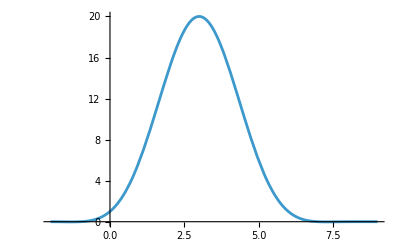

```mathematica
Plot[Binomial[6, x], {x, -2, 9}]
```

```mathematica
ComplexPlot3D[Binomial[z,9/ 90],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
With[{n= 90,m= 1680},Subsets[Range[n],{m}]]
```

{}

```mathematica
Length[]
```

2

```mathematica
With[{n= 90,m=1680},Binomial[n+m-1,m]]
```

71162162920101557449005619323655905095272767190081319967038913325166264544403318694292129532038634164043587090777592085678216167158666484580728410417570

```mathematica
With[{n= 90,m= 1680},DeleteDuplicates[Sort/@Tuples[Range[n],{m}]]]
```

Tuples::toomany: The length of the output of Tuples[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«40»},{1680}] should be a machine integer.

General::stop: Further output of Tuples::toomany will be suppressed during this calculation.

Tuples[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90},{1680}]

```mathematica
Length[]
```

2

```mathematica
With[{n= 90,m= 1680},Binomial[n+m,m]]
```

1399522537428663963163777180031899466873697754738265959351765295394936536039931934321078547463426471892857212785292644351671584620787107530087658738212210

```mathematica
With[{n= 90,m= 1680},Permutations[Join[ConstantArray[0,n],ConstantArray[1,m]]]]
```

Permutations::len: Permutations[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«1720»}] cannot be computed because its length is 1399522537428663963163777180031899466873697754738265959351765295394936536039931934321078547463426471892857212785292644351671584620787107530087658738212210, which is not a machine integer.

Permutations[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}]

```mathematica
Length[]
```

1

```mathematica
Buffer / Sum[Binomial[n,k]x^k,{k,0,n}]
```

(1+x)^-n (x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4+4 x^3 z+12 x^2 y z+12 x y^2 z+4 y^3 z+6 x^2 z^2+12 x y z^2+6 y^2 z^2+4 x z^3+4 y z^3+z^4)

```mathematica
Refrigerator = Expand[(1+x)^ 1680]
```

```mathematica
Refrigerator = Series[(90+x)^(1/ 90),{x,0, 90}]
```

3^(1/45) 10^(1/90)+x/(270 3^(44/45) 10^(89/90))-(89 x^2)/(4374000 (3^(44/45) 10^(89/90)))+(15931 x^3)/(106288200000 3^(44/45) 10^(89/90))-(4285439 x^4)/(3443737680000000 (3^(44/45) 10^(89/90)))+(1538472601 x^5)/(139471376040000000000 3^(44/45) 10^(89/90))-(690774197849 x^6)/(6778308875544000000000000 (3^(44/45) 10^(89/90)))+(53189613234373 x^7)/(54904301891906400000000000000 3^(44/45) 10^(89/90))-(33456266724420617 x^8)/(3557798762595534720000000000000000 (3^(44/45) 10^(89/90)))+(24055055774858423623 x^9)/(259363529793214481088000000000000000000 3^(44/45) 10^(89/90))-(19460540121860464711007 x^10)/(21008445913250372968128000000000000000000000 (3^(44/45) 10^(89/90)))+(1590456869959323434108663 x^11)/(170168411897328021041836800000000000000000000000 3^(44/45) 10^(89/90))-(1572961844389770876333467707 x^12)/(16540369636420283645266536960000000000000000000000000 (3^(44/45) 10^(89/90)))+(130555833084350982735677819681 x^13)/(133976994055004297526658949376000000000000000000000000000 3^(44/45) 10^(89/90))-(21802824125086614116858195886727 x^14)/(2170427303691069619931874979891200000000000000000000000000000 (3^(44/45) 10^(89/90)))+(27449755573484047173124468621389293 x^15)/(263706917398464958821722810056780800000000000000000000000000000000 3^(44/45) 10^(89/90))-(37029720268629979636544908170254156257 x^16)/(34176416494841058663295276183358791680000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(3134456909797561217469889579823278285519 x^17)/(276828973608212575172691737085206212608000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(4792584615080471101511461167549792498558551 x^18)/(40361664352077393460178455267023065798246400000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(408378657463962248070897664750690213429804951 x^19)/(326929481251826887027445487662886832965795840000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(697919125605911481953164109058929574751536661259 x^20)/(52962575962795955698446169001387666940458926080000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(179365215280719250861963176028144900711144921943563 x^21)/(1286990595895941723472241906733720306653151903744000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(30801899242298060443477130865196883403941159777399137 x^22)/(20849247653514255920250318889086268967781060840652800000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(2650302547848167896419184434009766619843458921716212701 x^23)/(168878905993465472954027583001598778639026592809287680000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(5483475971497859377691292593966207136456116509030844078369 x^24)/(32830059325129687942262962135510802567426769642125524992000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(11838824622463878396435500710373041207608755542997592365198671 x^25)/(6648087013338761808308249832440937519903920852530418810880000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(2048116659686250962583341622894536128916314708938583479179370083 x^26)/(107699009616087941294593647285543187822443517810992784736256000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(4790544867006141001482436055950320005535260104207346757800546624137 x^27)/(23553773403038432761127630661348295176768397345264122021819187200000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(1662319068851130927514405311414761041920735256159949324956789678575539 x^28)/(763142258258445221460535233427684763727296073986557553506941665280000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(144392473601241338152027137222544243606839038285065943088488041390751129 x^29)/(6181452291893406293830335390764246586191098199291116183406227488768000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(376719963625638651238638801013617931570243050885737045517865299988469695561 x^30)/(1502092906930097729400771499955711920444436862427741232567713279770624000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(32798941349212861925583423352766283784131806269051751156539304666738055107069 x^31)/(12166952546133791608146249149641266555599938585664703983798477566142054400000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(91476247422954671910452167730865165473943607684385333975588120715532435693615441 x^32)/(3153674099957878784831507779587016291211504081404291272600565385144020500480000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(23941828757335136402744708263378255581771240593031397865065290867274352941992623149 x^33)/(76634280628976454471405639043964495876439549178124277924193738858999698161664000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(4181369975325177645867590519645296518957577254159424721257579328525738463810358713493 x^34)/(1241475346189418562436771352512224833198320696685613302371938569515795110218956800000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(1827258679217102631244137057084994578784461260067668603189562166565747708685126757796441 x^35)/(50279751520671451778689239776745105744531988215767338746063512065389701963867750400000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(5754037580854656185787787592760647928592268507953088431443931262515539534649464160300992709 x^36)/(14661575543427795338665782318898872835105527763717755978352120118267637092663836016640000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(503711560118600848263963351701398341640820478304325768363429550251022501425124713924727442823 x^37)/(118758761901765142243192836783080869964354774886113823424652172957967860450577071734784000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(88255567559727485466880736727050267332752177488163183309571419620297574065486324876600929324093 x^38)/(1923891942808595304339723955885910093422547353155043939479365201919079339299348562103500800000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(23211214268208328677789633759214220308513822679386917210417283360138261979222903442546044412236459 x^39)/(46750574210248865895455292128027615270167900681667567729348574406633627944974170059115069440000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(81448150867143025330363824861082699062575003781968692491354247310725161285093168179894069842537734631 x^40)/(15147186044120632550127514649480947347534399820860291944308938107749295454171631099153282498560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(7149558413923115808877546479878942290883108258812324982350827709056094035732934445839969691787641632609 x^41)/(122692206957377123656032868660795673515028638548968364748902398672769293178790211903141588238336000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(3767817284137482031278466994896202587295398052394095265698886202672561556831256452957664027572087140384943 x^42)/(5962841258128528209683197416914669732830391833479862526796656575496587648489204298492681188383129600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(331129802715245223167472715667738362264867656744122930443630022323246747052681817109930520004532960546853479 x^43)/(48299014190841078498433899077008824835926173851186886467052918261522359952762554817790717625903349760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(116467382427753069857722903356225429418433905813001056171491323306240151304256904581665561990685274941434191841 x^44)/(1564888059783250943349258330095085924684008032778455121532514551673324462469506776096419251079268532224000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(461094367031474403566724974387296475067579833113671181382934148969404759013553085238813959921123003493137965498519 x^45)/(570401697790994968850804661319658819547320927947746891798601554084926766570135219887144817018393379995648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(81172656178714776523550844404094062067331771490315417974760885616396516054168540962259031466114219180161548795804497 x^46)/(9240507504214118495383035513378472876666599032753499647137345176175813618436190562171746035697972755929497600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(7148374977100009787893126489117985593546514940391819468032666075877982552089438107293407047622271344397630860975208789 x^47)/(74848110784134359812602587658365630300999452165303347141812495927024090309333143553591142889153579323028930560000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(30230477778155941393000031922479961075108211682917004530310144834887988212786233755743818404394585515457580911064157968681 x^48)/(29100945472871439095139886081572557061028587001869941368736698416426966312268726213636236355302911640793648201728000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(2664600684160316548497288528024305140477395229765684542171622766160841246755586603899133707930208466148189631732369352382311 x^49)/(235717658330258656670633077260737712194331554715146525086767257173058427129376682330453514477953584290428550433996800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(11748224416462835662324545120059161364364835568036903146434684776003149056945381336591280518264289127247368086308016474653609199 x^50)/(95465651623754755951606396290598773438704279659634342660140739155088662987397556343833673363571201637623562925768704000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(3109133038215664567341066382067421586957493836505766309165273341602245153364545331372010061863002163734465236488221536439211046253 x^51)/(2319815334457240569624035429861550194560513995729114526641419961468654510593760619155158262734780199794252579096179507200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(1097523962490129592271396432869799820195995324286535507135341489585592539137684501974319551837639763798266228480342202363041499327309 x^52)/(75162016836414594455818747927514226303760653461623310663182006751584406143237844060627127712606878473333783562716216033280000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(96892728688515403061091771875430063371642681553522634677099298674924292275947656315808324208458801034190333642632474808616437270801487 x^53)/(608812336374958215092131858212865233060461293039148816371774254687833689760226536891079734472115715634003646858001349869568000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(462081423115529957198346660073925972219363948328749444775086555380713949863994372970089898150140022132053701141714272362291789344452291503 x^54)/(266294515930406723281298474782307252940645769575323692281014059000458455901123087236158275858103414018313195135689790432949043200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(204113966810760005638796947390836936273989947720853959287467779326808098399013514387424255919230033412695357622508149946215982220426698583007 x^55)/(10784927895181472292892588228683443744096153667800609537381069389518567463995485033064410172253188267741684402995436512534436249600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(144308574535207323986629441805321713945710893038643749216239719984053325568102554671908948934895633622775617839113262011974699429841675898185949 x^56)/(698863327607759404579439717218687154617430757673479498022293296440803171666907430142573779162006599749661149314104286012231468974080000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(38272153004363668714138197750369269293286167895880308015822734157876037238824672262723641772786268306587702015331143540965290022472221307945210369 x^57)/(16982378860868553531280385128414097857203567411465551801941727103511517071505850552464542833636760373916765928332734150097224696070144000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(6768892164116595063269476422815309731216026039240348269419131155025730861997646346052053746642095522223735297814946042124516293974483554774171861469 x^58)/(275114537546070567206742239080308385286697792065741939191455979076886576558394778949925593904915518057451608038990293231575040076336332800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(598760139059737451444125380519883076054515930488057247764380432170835413029927394577045228876696551364163974903325481251658483699200502921464456695029 x^59)/(2228427754123171594374612136550497920822252115732509707450793430522781270122997709494397310629815696265358025115821375175757824618324295680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(3178817578268146129716861645180059250773425074961095928381095714394965207775884537809533120106381991192346542761754979965054889959055470010054800593908961 x^60)/(1083015888503861394866061498363541989519614528245999717821085607234071697279776886814277092966090428384964000206289188335418302764505607700480000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(281351411558520015644939934792248194998782327536310769136549766590465855029213124912027365827120596236843917776569100603792317227687548894824358498467450499 x^61)/(8772428696881277298415098136744690115108877678792597714350793418595980747966192783195644453025332469918208401670942425516888252392495422373888000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(49817351549829560189518558131440333624139232124090639090016828026292486395333898149745748742744030733678589183083477200458581589121837286570674316067349541581 x^62)/(142113344889476692234324589815263979864763818396440082972482853381254888117052323087769440139010386012674976107069267293373589688758425842456985600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(39704429185214159471046290830757945898438968002900239354743411936955111657081116825347361747966992494741835578917531328765489526530104317396827429905677584640057 x^63)/(10360062842442850863882262597532744132141282361100482048694000011493481343733114353098392186133857140324005758205349585686934688310489243915114250240000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(225084409050979070041361422719566795298250509608441456902040402270598527983992851282894193749224880452691465896883485102771560125899161375322614700135286227324483133 x^64)/(5370656577522373887836564930560974558102040775994489894042969605958220728591246480646206509291791541543964585053653225220106942420157624045595227324416000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(99712393209583728028323110264768090317124975756539565407603898205875147896908833118322127830906622040542319392319383900527801135773328489267918312159931798704746027919 x^65)/(217511591389656142457380879687719469603132651427776840708740269041307939507945482466171363626317557432530565694672955621414331168016383773846606706638848000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(53019798898441384112514715630784414569533089381818174369915927327833067277183614991733284152997530210466547829606916039471555349376199848520732200711221917329459956118021 x^66)/(10571063341537288523428710752823166222712246859389954458444777075407565860086150447855928272239033291220985492761105643200736494765596251408945085942648012800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(4699769935191692242451117852704905046693388325949524441536278991044784874017813275162745889323169133133743694925902602364501003282764938811412366269014133836114368349028757 x^67)/(85625613066452037039772557097867646403969199561058631113402694310801283466697818627633019005136169658889982491364955709925965607601329636412455196135448903680000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(1666759584662983089984575854938698383912614012773510756354248590412294588556082131526834998042905100215490631571074517038563326399517048005529715072699188993996089810370257409 x^68)/(2774269863353046000088630849970911743488602065778299648074247295669961584321009323535309815766411896948035432720224565001601285686283080219763548354788544479232000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(443430517328382327287635637233473713528751528007004883397028135857949155972811589687508841435849404705155964112321955206911695401680209423732014196949840758880959719550243699377 x^69)/(67414757679479017802153729654293155366773030198412681448204209284780066499000526561908028523123809095837261015101456929538911242176678849340254225021361630845337600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(393322868870275124304132810226091183900002605342213331573163956506000901347883880052820342353598421973473340167629574268530673821290345758850296592694508753127411271241066161347399 x^70)/(5460595372037800441974452101997745584708615446071427197304540952067185386419042651514550310373028536762818142223218011292651810616310986796560592226730292098472345600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(34894940155124831098475106642452793906846710014797208106751545944102812360427050147221342767398823380435331967829558990386967808455040675140817158272995924449993853486584165497567131 x^71)/(44230822513506183579993062026181739236139785113178560298166781711744201629994245477267857514021531147778826952008065891470479665992118993052140797036515365997625999360000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(222943772651092545888157456338630900270843630284539362594035627036872868170768423390597158940911082577601335942463052389582337328219254873474680824206170961311010729925786233363956399959 x^72)/(25795415689876806263851953773669190322516722678005736365890867094289218390612643962342614502177356965384611878411104027905583741206603796748008512831695761449815482826752000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(19787023328855186367251673419424515107599943570048363428037764761258894696964501577365465654495382246853137747550933101809643336294966470208800781644270981621014226290262589122809226237457 x^73)/(208942867088002130737200825566720441612385453691846464563716023463742668963962416094975177467636591419615356215129942626035228303773490753658868953936735667743505410896691200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(3512998817493235655310168721410801074103352143558045928615677749100261601739454347613884969848112594042655726044921068805068839895179317373016549584357191304552498716236079674263075869023109 x^74)/(3384874446825634517942653374180871154120644349807912725932199580112631237216191140738597874975712780997768770685105070541770698521130550209273677053775117817444787656526397440000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(23393059125687456228710413515874524352454221923953027838651798131258642005983026500760860014218581763730044479733129397172953404861999074386917203682234536897015088951416054550917822211824882831 x^75)/(2056311226446572969650161924814879226128291442508306981003811244918423476608836117998698209047745514456144528191201330354125699351586809252133758810168384074097708501339786444800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(8309460844171823267766662148349324466037554934987314993845315030940240784125233992296581275576905701232319483879941594816855922600717460686173905665863204711471307122795102745481283268821375485601 x^76)/(66624483736868964216665246364002086926556642737269146184523484335356920642126290223157821973146954668379082713394923103473672658991412619769133785449455644000765755443409080811520000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(738031204068715575691638992630662727574426470134782431726079344111692295099123055497614536930785170009452375977336630739642566943718269008217445985049850091191587914451892307485019432148953077221107 x^77)/(539658318268638610154988495548416904105108806171880084094640223116391057201222950807578357982490332813870569978498877138136748537830442220129983662140590716406202619091613554573312000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(393370631768625401843643583072143233797169308581839036110000290411531993287832588580228548184108495615038116395920424184229488181001837381379898710031570098605116358402858599889515357335391990158850031 x^78)/(26227394267855836453532440883653061539508287979953372086999514843456605379979435409248308197949030174754109700955045428913445978938559491898317205980032708817341447287852418752262963200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(34950233726379515133424484931435105797751030087796559423494835929095481783383505560058533920307057350910791632695765282900085791676606285821588722097615069900117869868729930539550737887811599733227447691 x^79)/(212441893569632275273612771157589798470017132637622313904696070231998503577833426814911296403387144415508288577735867974198912429402331884376369368438264941420465723031604591893330001920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(248461211560831973083514663377572167116212072894145740941624788619939779998073341026456117639462870707624817716834195396136709893028994085905674225391945531919937936896801076205666195644452662503513925635319 x^80)/(137662347033121714377301075710118189408571101949179259410243053510335030318436060576062520069394869581249370998372842447280895254252711061075887350747995682040461788524479775546877841244160000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(1788672262026429374228222061655142031069610712764955189038756853274946476206129982049457590886493206224191062743489372656788174519915728424434948748596615884291633207720070947604590942444414717362796750648661481 x^81)/(90320265888431156802947235773408544070963499988856512099060467408130813391925899343954619417529973932257712312032421929660995376315203727171889690825759966986746979450911180736306551640293376000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(317991027266113261189012453839130006450399816715701423729353626915148411343084913150207228779796316589466552593592537495008024489650384011846496132402944711721993035391990174075362521450666801825790866231173013049 x^82)/(1463188307392584740207745219529218413949608699819475496004779572011719176949199569372064834563985577702574939454925235260508125096306300380184612991377311465185301067104761127928166136572752691200000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(28270551689116262100165336106975184549367472861989889225287956783215423220489440652233483628507433977273177007085775110550171237459399802691750541698811193105982971182620427644603615009451449767138684360479827268537 x^83)/(11851825289879936395682736278186669152991830468537751517638714533294925333288516511913725159968283179390857009584894405610115813280081033079495365230156222868000938643548565136218145706239296798720000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(30164678652287051660876413626142521914175093543743211803382249887690856576262233175933127031617432053750479866560522042957032710369179589472097827992631543044083830251855996296792057215084696901536976212631975695528979 x^84)/(1151997418176329817660361966239744241670805921541869447514483052636266742395643804958014085548917125036791301331651736225303257050823876415326949500371184862769691236152920531240403762646459648835584000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(13412635643096342559092047682353607244073501888067937530692142758885599109409777680992853366588009934958816312431234477806600603392978148048211028340958931404131157227869380941614774146401483757571647246546182604853150133 x^85)/(46655895436141357615244659632709641787667639822445712624336563631768803067023574100799570464731143563990047703931895317124781910558366994820741454765032986942172495064193281515236352387181615777841152000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(2385889535675440098476629598193552135114377114926317538889865115411998781113381150742193846535620650988371766832244477226574139891927671033041073390232438751399981898510997554009567615019184866550361157879808156849342915519 x^86)/(755825506065489993366963486049896196960215765123620544514252330834654609685781900432953041528644525736638772803696704137421466951045545316096011567193534388463194420039931160546828908672342175601026662400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(636703417813525204210711602083444826677591879048785221843747107868050295415050231917028902701350628206862382879818621008843354090469939521541547136793408396451188272847469312775173923194257644214939482787304666408864304248329 x^87)/(18366559797391406838817212711012477586133243092503979231696331639282107015364500180520758909146061975400322179129829910539341646910406751181133081082802885639655624406970327201287942480737914867104947896320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(453159187096553529433241921155571777096260620097539954710426918863542342073129842334401752658988551657411417778736362170748601743117196046740797503086872212346941180738439749974257876789803917868978291885618930301363512541833431 x^88)/(1190153074870963163155355383673608547581434152394257854213922290225480534595619611697745177312664816005940877207612978202949338719794357476537423654165626989449684461571677202643458672751816883388400623681536000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+(40320984299074240444739806445291830368823458994970998891594053600903278728956350802765477295578992590730797948200148899215260418019607589821801971089269000557027272025479824494900540744926485680948753858901306843331434335042460001 x^89)/(9640239906454801621558378607756229235409616634393488619132770550826392330224518854751735936232585009648121105381665123443889643630334295559953131598741578614542444138730585341412015249289716755446045051820441600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 3^(44/45) 10^(89/90))-(322930763251285591721921109820342269423907083090722730122776775289634359340211413579348707660292151659162960767134992533815020687919037186882811986453955425461231421652067914379658430826116223818718569655940566508241457589355062148009 x^90)/(7027734891805550382116058005054291112613610526472853203347789731552440008733674245114015497513554472033480285823233874990595550206513701463205832935482610810001441777134596713889359116732203514720166842777101926400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 (3^(44/45) 10^(89/90)))+O[x]^91

```mathematica
Buffer / Sum[Binomial[1/90,k]x^k,{k,0,90}]
```

(x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4+4 x^3 z+12 x^2 y z+12 x y^2 z+4 y^3 z+6 x^2 z^2+12 x y z^2+6 y^2 z^2+4 x z^3+4 y z^3+z^4)/(1+x/90-(89 x^2)/16200+(15931 x^3)/4374000-(4285439 x^4)/1574640000+(1538472601 x^5)/708588000000-(690774197849 x^6)/382637520000000+(53189613234373 x^7)/34437376800000000-(33456266724420617 x^8)/24794911296000000000+(24055055774858423623 x^9)/20083878149760000000000-(19460540121860464711007 x^10)/18075490334784000000000000+(1590456869959323434108663 x^11)/1626794130130560000000000000-(1572961844389770876333467707 x^12)/1756937660541004800000000000000+(130555833084350982735677819681 x^13)/158124389448690432000000000000000-(21802824125086614116858195886727 x^14)/28462390100764277760000000000000000+(27449755573484047173124468621389293 x^15)/38424226636031774976000000000000000000-(37029720268629979636544908170254156257 x^16)/55330886355885755965440000000000000000000+(3134456909797561217469889579823278285519 x^17)/4979779772029718036889600000000000000000000-(4792584615080471101511461167549792498558551 x^18)/8067243230688143219761152000000000000000000000+(408378657463962248070897664750690213429804951 x^19)/726051890761932889778503680000000000000000000000-(697919125605911481953164109058929574751536661259 x^20)/1306893403371479201601306624000000000000000000000000+(179365215280719250861963176028144900711144921943563 x^21)/352861218910299384432352788480000000000000000000000000-(30801899242298060443477130865196883403941159777399137 x^22)/63515019403853889197823501926400000000000000000000000000+(2650302547848167896419184434009766619843458921716212701 x^23)/5716351746346850027804115173376000000000000000000000000000-(5483475971497859377691292593966207136456116509030844078369 x^24)/12347319772109196060056888774492160000000000000000000000000000+(11838824622463878396435500710373041207608755542997592365198671 x^25)/27781469487245691135127999742607360000000000000000000000000000000-(2048116659686250962583341622894536128916314708938583479179370083 x^26)/5000664507704224404323039953669324800000000000000000000000000000000+(4790544867006141001482436055950320005535260104207346757800546624137 x^27)/12151614753721265302504987087416459264000000000000000000000000000000000-(1662319068851130927514405311414761041920735256159949324956789678575539 x^28)/4374581311339655508901795351469925335040000000000000000000000000000000000+(144392473601241338152027137222544243606839038285065943088488041390751129 x^29)/393712318020568995801161581632293280153600000000000000000000000000000000000-(376719963625638651238638801013617931570243050885737045517865299988469695561 x^30)/1063023258655536288663136270407191856414720000000000000000000000000000000000000+(32798941349212861925583423352766283784131806269051751156539304666738055107069 x^31)/95672093278998265979682264336647267077324800000000000000000000000000000000000000-(91476247422954671910452167730865165473943607684385333975588120715532435693615441 x^32)/275535628643515006021484921289544129182695424000000000000000000000000000000000000000+(23941828757335136402744708263378255581771240593031397865065290867274352941992623149 x^33)/74394619733749051625800928748176914879327764480000000000000000000000000000000000000000-(4181369975325177645867590519645296518957577254159424721257579328525738463810358713493 x^34)/13391031552074829292644167174671844678278997606400000000000000000000000000000000000000000+(1827258679217102631244137057084994578784461260067668603189562166565747708685126757796441 x^35)/6025964198433673181689875228602330105225548922880000000000000000000000000000000000000000000-(5754037580854656185787787592760647928592268507953088431443931262515539534649464160300992709 x^36)/19524124002925101108675195740671549540930778510131200000000000000000000000000000000000000000000+(503711560118600848263963351701398341640820478304325768363429550251022501425124713924727442823 x^37)/1757171160263259099780767616660439458683770065911808000000000000000000000000000000000000000000000-(88255567559727485466880736727050267332752177488163183309571419620297574065486324876600929324093 x^38)/316290808847386637960538170998879102563078611864125440000000000000000000000000000000000000000000000+(23211214268208328677789633759214220308513822679386917210417283360138261979222903442546044412236459 x^39)/85398518388794392249345306169697357692031225203313868800000000000000000000000000000000000000000000000-(81448150867143025330363824861082699062575003781968692491354247310725161285093168179894069842537734631 x^40)/307434666199659812097643102210910487691312410731929927680000000000000000000000000000000000000000000000000+(7149558413923115808877546479878942290883108258812324982350827709056094035732934445839969691787641632609 x^41)/27669119957969383088787879198981943892218116965873693491200000000000000000000000000000000000000000000000000-(3767817284137482031278466994896202587295398052394095265698886202672561556831256452957664027572087140384943 x^42)/14941324777303466867945454767450249701797783161571794485248000000000000000000000000000000000000000000000000000+(331129802715245223167472715667738362264867656744122930443630022323246747052681817109930520004532960546853479 x^43)/1344719229957312018115090929070522473161800484541461503672320000000000000000000000000000000000000000000000000000-(116467382427753069857722903356225429418433905813001056171491323306240151304256904581665561990685274941434191841 x^44)/484098922784632326521432734465388090338248174434926141322035200000000000000000000000000000000000000000000000000000+(461094367031474403566724974387296475067579833113671181382934148969404759013553085238813959921123003493137965498519 x^45)/1960600637277760922411802574584821765869905106461450872354242560000000000000000000000000000000000000000000000000000000-(81172656178714776523550844404094062067331771490315417974760885616396516054168540962259031466114219180161548795804497 x^46)/352908114709996966034124463425267917856582919163061157023763660800000000000000000000000000000000000000000000000000000000+(7148374977100009787893126489117985593546514940391819468032666075877982552089438107293407047622271344397630860975208789 x^47)/31761730323899726943071201708274112607092462724675504132138729472000000000000000000000000000000000000000000000000000000000-(30230477778155941393000031922479961075108211682917004530310144834887988212786233755743818404394585515457580911064157968681 x^48)/137210674999246820394067591379744166462639438970598177850839311319040000000000000000000000000000000000000000000000000000000000+(2664600684160316548497288528024305140477395229765684542171622766160841246755586603899133707930208466148189631732369352382311 x^49)/12348960749932213835466083224176974981637549507353836006575538018713600000000000000000000000000000000000000000000000000000000000-(11748224416462835662324545120059161364364835568036903146434684776003149056945381336591280518264289127247368086308016474653609199 x^50)/55570323374694962259597374508796387417368972783092262029589921084211200000000000000000000000000000000000000000000000000000000000000+(3109133038215664567341066382067421586957493836505766309165273341602245153364545331372010061863002163734465236488221536439211046253 x^51)/15003987311167639810091291117375024602689622651434910747989278692737024000000000000000000000000000000000000000000000000000000000000000-(1097523962490129592271396432869799820195995324286535507135341489585592539137684501974319551837639763798266228480342202363041499327309 x^52)/5401435432020350331632864802255008856968264154516567869276140329385328640000000000000000000000000000000000000000000000000000000000000000+(96892728688515403061091771875430063371642681553522634677099298674924292275947656315808324208458801034190333642632474808616437270801487 x^53)/486129188881831529846957832202950797127143773906491108234852629644679577600000000000000000000000000000000000000000000000000000000000000000-(462081423115529957198346660073925972219363948328749444775086555380713949863994372970089898150140022132053701141714272362291789344452291503 x^54)/2362587857965701235056215064506340874037918741185546786021383780073142747136000000000000000000000000000000000000000000000000000000000000000000+(204113966810760005638796947390836936273989947720853959287467779326808098399013514387424255919230033412695357622508149946215982220426698583007 x^55)/1063164536084565555775296779027853393317063433533496053709622701032914236211200000000000000000000000000000000000000000000000000000000000000000000-(144308574535207323986629441805321713945710893038643749216239719984053325568102554671908948934895633622775617839113262011974699429841675898185949 x^56)/765478465980887200158213680900054443188285672144117158670928344743698250072064000000000000000000000000000000000000000000000000000000000000000000000+(38272153004363668714138197750369269293286167895880308015822734157876037238824672262723641772786268306587702015331143540965290022472221307945210369 x^57)/206679185814839544042717693843014699660837131478911632841150653080798527519457280000000000000000000000000000000000000000000000000000000000000000000000-(6768892164116595063269476422815309731216026039240348269419131155025730861997646346052053746642095522223735297814946042124516293974483554774171861469 x^58)/37202253446671117927689184891742645938950683666204093911407117554543734953502310400000000000000000000000000000000000000000000000000000000000000000000000+(598760139059737451444125380519883076054515930488057247764380432170835413029927394577045228876696551364163974903325481251658483699200502921464456695029 x^59)/3348202810200400613492026640256838134505561529958368452026640579908936145815207936000000000000000000000000000000000000000000000000000000000000000000000000-(3178817578268146129716861645180059250773425074961095928381095714394965207775884537809533120106381991192346542761754979965054889959055470010054800593908961 x^60)/18080295175082163312856943857386925926330032261775189640943859131508255187402122854400000000000000000000000000000000000000000000000000000000000000000000000000+(281351411558520015644939934792248194998782327536310769136549766590465855029213124912027365827120596236843917776569100603792317227687548894824358498467450499 x^61)/1627226565757394698157124947164823333369702903559767067684947321835742966866191056896000000000000000000000000000000000000000000000000000000000000000000000000000-(49817351549829560189518558131440333624139232124090639090016828026292486395333898149745748742744030733678589183083477200458581589121837286570674316067349541581 x^62)/292900781836331045668282490489668200006546522640758072183290517930433734035914390241280000000000000000000000000000000000000000000000000000000000000000000000000000+(39704429185214159471046290830757945898438968002900239354743411936955111657081116825347361747966992494741835578917531328765489526530104317396827429905677584640057 x^63)/237249633287428146991308817296631242005302683339014038468465319523651324569090656095436800000000000000000000000000000000000000000000000000000000000000000000000000000-(225084409050979070041361422719566795298250509608441456902040402270598527983992851282894193749224880452691465896883485102771560125899161375322614700135286227324483133 x^64)/1366557887735586126669938787628595953950543456032720861578360240456231629517962179109715968000000000000000000000000000000000000000000000000000000000000000000000000000000+(99712393209583728028323110264768090317124975756539565407603898205875147896908833118322127830906622040542319392319383900527801135773328489267918312159931798704746027919 x^65)/614951049481013757001472454432868179277744555214724387710262108205304233283082980599372185600000000000000000000000000000000000000000000000000000000000000000000000000000000-(53019798898441384112514715630784414569533089381818174369915927327833067277183614991733284152997530210466547829606916039471555349376199848520732200711221917329459956118021 x^66)/332073566719747428780795125393748816809982059815951169363541538430864285972864809523660980224000000000000000000000000000000000000000000000000000000000000000000000000000000000+(4699769935191692242451117852704905046693388325949524441536278991044784874017813275162745889323169133133743694925902602364501003282764938811412366269014133836114368349028757 x^67)/29886621004777268590271561285437393512898385383435605242718738458777785737557832857129488220160000000000000000000000000000000000000000000000000000000000000000000000000000000000-(1666759584662983089984575854938698383912614012773510756354248590412294588556082131526834998042905100215490631571074517038563326399517048005529715072699188993996089810370257409 x^68)/10759183561719816692497762062757461664643418738036817887378745845160002865520819828566615759257600000000000000000000000000000000000000000000000000000000000000000000000000000000000+(443430517328382327287635637233473713528751528007004883397028135857949155972811589687508841435849404705155964112321955206911695401680209423732014196949840758880959719550243699377 x^69)/2904979561664350506974395756944514649453723059269940829592261378193200773690621353712986254999552000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(393322868870275124304132810226091183900002605342213331573163956506000901347883880052820342353598421973473340167629574268530673821290345758850296592694508753127411271241066161347399 x^70)/2614481605497915456276956181250063184508350753342946746633035240373880696321559218341687629499596800000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(34894940155124831098475106642452793906846710014797208106751545944102812360427050147221342767398823380435331967829558990386967808455040675140817158272995924449993853486584165497567131 x^71)/235303344494812391064926056312505686605751567800865207196973171633649262668940329650751886654963712000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(222943772651092545888157456338630900270843630284539362594035627036872868170768423390597158940911082577601335942463052389582337328219254873474680824206170961311010729925786233363956399959 x^72)/1524765672326384294100720844905036849205270159349606542636386152186047222094733336136872225524164853760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(19787023328855186367251673419424515107599943570048363428037764761258894696964501577365465654495382246853137747550933101809643336294966470208800781644270981621014226290262589122809226237457 x^73)/137228910509374586469064876041453316428474314341464588837274753696744249988526000252318500297174836838400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(3512998817493235655310168721410801074103352143558045928615677749100261601739454347613884969848112594042655726044921068805068839895179317373016549584357191304552498716236079674263075869023109 x^74)/24701203891687425564431677687461596957125376581463625990709455665413964997934680045417330053491470630912000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(23393059125687456228710413515874524352454221923953027838651798131258642005983026500760860014218581763730044479733129397172953404861999074386917203682234536897015088951416054550917822211824882831 x^75)/166733126268890122559913824390365779460596291924879475437288825741544263736059090306566977861067426758656000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(8309460844171823267766662148349324466037554934987314993845315030940240784125233992296581275576905701232319483879941594816855922600717460686173905665863204711471307122795102745481283268821375485601 x^76)/60023925456800444121568976780531680605814665092956611157423977266955934944981272510364112029984273633116160000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(738031204068715575691638992630662727574426470134782431726079344111692295099123055497614536930785170009452375977336630739642566943718269008217445985049850091191587914451892307485019432148953077221107 x^77)/5402153291112039970941207910247851254523319858366095004168157954026034145048314525932770082698584626980454400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(393370631768625401843643583072143233797169308581839036110000290411531993287832588580228548184108495615038116395920424184229488181001837381379898710031570098605116358402858599889515357335391990158850031 x^78)/2917162777200501584308252271533839677442592723517691302250805295174058438326089844003695844657235698569445376000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(34950233726379515133424484931435105797751030087796559423494835929095481783383505560058533920307057350910791632695765282900085791676606285821588722097615069900117869868729930539550737887811599733227447691 x^79)/262544649948045142587742704438045570969833345116592217202572476565665259449348085960332626019151212871250083840000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(248461211560831973083514663377572167116212072894145740941624788619939779998073341026456117639462870707624817716834195396136709893028994085905674225391945531919937936896801076205666195644452662503513925635319 x^80)/1890321479625925026631747471953928110982800084839463963858521831272789868035306218914394907337888732673000603648000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(1788672262026429374228222061655142031069610712764955189038756853274946476206129982049457590886493206224191062743489372656788174519915728424434948748596615884291633207720070947604590942444414717362796750648661481 x^81)/13780443586472993444145439070544135929064612618479692296528624149978638137977382335885938874493208861186174400593920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(317991027266113261189012453839130006450399816715701423729353626915148411343084913150207228779796316589466552593592537495008024489650384011846496132402944711721993035391990174075362521450666801825790866231173013049 x^82)/2480479845565138819946179032697944467231630271326344613375152346996154864835928820459468997408777595013511392106905600000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(28270551689116262100165336106975184549367472861989889225287956783215423220489440652233483628507433977273177007085775110550171237459399802691750541698811193105982971182620427644603615009451449767138684360479827268537 x^83)/223243186100862493795156112942815002050846724419371015203763711229653937835233593841352209766789983551216025289621504000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(30164678652287051660876413626142521914175093543743211803382249887690856576262233175933127031617432053750479866560522042957032710369179589472097827992631543044083830251855996296792057215084696901536976212631975695528979 x^84)/241102640988931493298768601978240202214914462372920696420064808128026252862052281348660386548133182235313307312791224320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(13412635643096342559092047682353607244073501888067937530692142758885599109409777680992853366588009934958816312431234477806600603392978148048211028340958931404131157227869380941614774146401483757571647246546182604853150133 x^85)/108496188445019171984445870890208090996711508067814313389029163657611813787923526606897173946659932005890988290756050944000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(2385889535675440098476629598193552135114377114926317538889865115411998781113381150742193846535620650988371766832244477226574139891927671033041073390232438751399981898510997554009567615019184866550361157879808156849342915519 x^86)/19529313920103450957200256760237456379408071452206576410025249458370126481826234789241491310398787761060377892336089169920000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(636703417813525204210711602083444826677591879048785221843747107868050295415050231917028902701350628206862382879818621008843354090469939521541547136793408396451188272847469312775173923194257644214939482787304666408864304248329 x^87)/5272914758427931758444069325264113222440179292095775630706817353759934150093083393095202653807672695486302030930744075878400000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(453159187096553529433241921155571777096260620097539954710426918863542342073129842334401752658988551657411417778736362170748601743117196046740797503086872212346941180738439749974257876789803917868978291885618930301363512541833431 x^88)/3796498626068110866079729914190161520156929090308958454108908494707152588067020043028545910741524340750137462270135734632448000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000+(40320984299074240444739806445291830368823458994970998891594053600903278728956350802765477295578992590730797948200148899215260418019607589821801971089269000557027272025479824494900540744926485680948753858901306843331434335042460001 x^89)/341684876346129977947175692277114536814123618127806260869801764523643732926031803872569131966737190667512371604312216116920320000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-(322930763251285591721921109820342269423907083090722730122776775289634359340211413579348707660292151659162960767134992533815020687919037186882811986453955425461231421652067914379658430826116223818718569655940566508241457589355062148009 x^90)/2767647498403652821372123107444627748194401306835230713045394292641514236700857611367809968930571244406850209994928950547054592000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000)

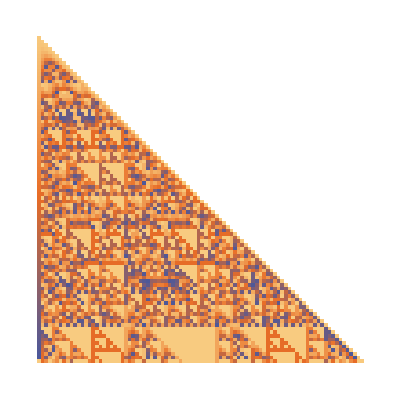

```mathematica
Refrigerator =ArrayPlot[Table[Mod[Binomial[i,j], 90],{i, 90},{j,i}],PlotTheme->"Scientific"]
```

```mathematica
Refrigerator = Plot3D[Binomial[n,k],{n,-90, 90},{k,-90, 90}]
```

-Graphics3D-

```mathematica
Refrigerator = Plot3D[Log[Binomial[n,k]],{n,1,12},{k,1,12},RegionFunction->(#2<=#1&)]
```

-Graphics3D-

```mathematica
Refrigerator =Buffer /Sum[Binomial[90,k] D[f[z],{z,k}]D[g[z],{z,90-k}],{k,0,90}]
```

(x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4+4 x^3 z+12 x^2 y z+12 x y^2 z+4 y^3 z+6 x^2 z^2+12 x y z^2+6 y^2 z^2+4 x z^3+4 y z^3+z^4)/(103827421287553411369671120 f^(45)[z] g^(45)[z]+101570303433476163296417400 g^(44)[z] f^(46)[z]+101570303433476163296417400 f^(44)[z] g^(46)[z]+95087092576020237979624800 g^(43)[z] f^(47)[z]+95087092576020237979624800 f^(43)[z] g^(47)[z]+85182187099351463190080550 g^(42)[z] f^(48)[z]+85182187099351463190080550 f^(42)[z] g^(48)[z]+73013303228015539877211900 g^(41)[z] f^(49)[z]+73013303228015539877211900 f^(41)[z] g^(49)[z]+59870908646972742699313758 g^(40)[z] f^(50)[z]+59870908646972742699313758 f^(40)[z] g^(50)[z]+46957575409390386430834320 g^(39)[z] f^(51)[z]+46957575409390386430834320 f^(39)[z] g^(51)[z]+35218181557042789823125740 g^(38)[z] f^(52)[z]+35218181557042789823125740 f^(38)[z] g^(52)[z]+25250771682408037986392040 g^(37)[z] f^(53)[z]+25250771682408037986392040 f^(37)[z] g^(53)[z]+17301454671279581583268620 g^(36)[z] f^(54)[z]+17301454671279581583268620 f^(36)[z] g^(54)[z]+11324588512110271581775824 g^(35)[z] f^(55)[z]+11324588512110271581775824 f^(35)[z] g^(55)[z]+7077867820068919738609890 g^(34)[z] f^(56)[z]+7077867820068919738609890 f^(34)[z] g^(56)[z]+4221886068111285458118180 g^(33)[z] f^(57)[z]+4221886068111285458118180 f^(33)[z] g^(57)[z]+2402107590477110691687930 g^(32)[z] f^(58)[z]+2402107590477110691687930 f^(32)[z] g^(58)[z]+1302838015174026137864640 g^(31)[z] f^(59)[z]+1302838015174026137864640 f^(31)[z] g^(59)[z]+673132974506580171230064 g^(30)[z] f^(60)[z]+673132974506580171230064 f^(30)[z] g^(60)[z]+331049003855695166178720 g^(29)[z] f^(61)[z]+331049003855695166178720 f^(29)[z] g^(61)[z]+154845501803470319664240 g^(28)[z] f^(62)[z]+154845501803470319664240 f^(28)[z] g^(62)[z]+68820223023764586517440 g^(27)[z] f^(63)[z]+68820223023764586517440 f^(27)[z] g^(63)[z]+29033531588150684937045 g^(26)[z] f^(64)[z]+29033531588150684937045 f^(26)[z] g^(64)[z]+11613412635260273974818 g^(25)[z] f^(65)[z]+11613412635260273974818 f^(25)[z] g^(65)[z]+4399019937598588626825 g^(24)[z] f^(66)[z]+4399019937598588626825 f^(24)[z] g^(66)[z]+1575768335856210851400 g^(23)[z] f^(67)[z]+1575768335856210851400 f^(23)[z] g^(67)[z]+532980466539600729150 g^(22)[z] f^(68)[z]+532980466539600729150 f^(22)[z] g^(68)[z]+169935800925669797700 g^(21)[z] f^(69)[z]+169935800925669797700 f^(21)[z] g^(69)[z]+50980740277700939310 g^(20)[z] f^(70)[z]+50980740277700939310 f^(20)[z] g^(70)[z]+14360771909211532200 g^(19)[z] f^(71)[z]+14360771909211532200 f^(19)[z] g^(71)[z]+3789648142708598775 g^(18)[z] f^(72)[z]+3789648142708598775 f^(18)[z] g^(72)[z]+934433788613079150 g^(17)[z] f^(73)[z]+934433788613079150 f^(17)[z] g^(73)[z]+214667221708410075 g^(16)[z] f^(74)[z]+214667221708410075 f^(16)[z] g^(74)[z]+45795673964460816 g^(15)[z] f^(75)[z]+45795673964460816 f^(15)[z] g^(75)[z]+9038619861406740 g^(14)[z] f^(76)[z]+9038619861406740 f^(14)[z] g^(76)[z]+1643385429346680 g^(13)[z] f^(77)[z]+1643385429346680 f^(13)[z] g^(77)[z]+273897571557780 g^(12)[z] f^(78)[z]+273897571557780 f^(12)[z] g^(78)[z]+41604694413840 g^(11)[z] f^(79)[z]+41604694413840 f^(11)[z] g^(79)[z]+5720645481903 g^(10)[z] f^(80)[z]+5720645481903 f^(10)[z] g^(80)[z]+706252528630 g^(9)[z] f^(81)[z]+706252528630 f^(9)[z] g^(81)[z]+77515521435 g^(8)[z] f^(82)[z]+77515521435 f^(8)[z] g^(82)[z]+7471375560 g^(7)[z] f^(83)[z]+7471375560 f^(7)[z] g^(83)[z]+622614630 g^(6)[z] f^(84)[z]+622614630 f^(6)[z] g^(84)[z]+43949268 g^(5)[z] f^(85)[z]+43949268 f^(5)[z] g^(85)[z]+2555190 g^(4)[z] f^(86)[z]+2555190 f^(4)[z] g^(86)[z]+117480 g^(3)[z] f^(87)[z]+117480 f^(3)[z] g^(87)[z]+4005 g''[z] f^(88)[z]+4005 f''[z] g^(88)[z]+90 g'[z] f^(89)[z]+90 f'[z] g^(89)[z]+g[z] f^(90)[z]+f[z] g^(90)[z])

```mathematica
Refrigerator =D[f[z] g[z],{z,90}]
```

103827421287553411369671120 f^(45)[z] g^(45)[z]+101570303433476163296417400 g^(44)[z] f^(46)[z]+101570303433476163296417400 f^(44)[z] g^(46)[z]+95087092576020237979624800 g^(43)[z] f^(47)[z]+95087092576020237979624800 f^(43)[z] g^(47)[z]+85182187099351463190080550 g^(42)[z] f^(48)[z]+85182187099351463190080550 f^(42)[z] g^(48)[z]+73013303228015539877211900 g^(41)[z] f^(49)[z]+73013303228015539877211900 f^(41)[z] g^(49)[z]+59870908646972742699313758 g^(40)[z] f^(50)[z]+59870908646972742699313758 f^(40)[z] g^(50)[z]+46957575409390386430834320 g^(39)[z] f^(51)[z]+46957575409390386430834320 f^(39)[z] g^(51)[z]+35218181557042789823125740 g^(38)[z] f^(52)[z]+35218181557042789823125740 f^(38)[z] g^(52)[z]+25250771682408037986392040 g^(37)[z] f^(53)[z]+25250771682408037986392040 f^(37)[z] g^(53)[z]+17301454671279581583268620 g^(36)[z] f^(54)[z]+17301454671279581583268620 f^(36)[z] g^(54)[z]+11324588512110271581775824 g^(35)[z] f^(55)[z]+11324588512110271581775824 f^(35)[z] g^(55)[z]+7077867820068919738609890 g^(34)[z] f^(56)[z]+7077867820068919738609890 f^(34)[z] g^(56)[z]+4221886068111285458118180 g^(33)[z] f^(57)[z]+4221886068111285458118180 f^(33)[z] g^(57)[z]+2402107590477110691687930 g^(32)[z] f^(58)[z]+2402107590477110691687930 f^(32)[z] g^(58)[z]+1302838015174026137864640 g^(31)[z] f^(59)[z]+1302838015174026137864640 f^(31)[z] g^(59)[z]+673132974506580171230064 g^(30)[z] f^(60)[z]+673132974506580171230064 f^(30)[z] g^(60)[z]+331049003855695166178720 g^(29)[z] f^(61)[z]+331049003855695166178720 f^(29)[z] g^(61)[z]+154845501803470319664240 g^(28)[z] f^(62)[z]+154845501803470319664240 f^(28)[z] g^(62)[z]+68820223023764586517440 g^(27)[z] f^(63)[z]+68820223023764586517440 f^(27)[z] g^(63)[z]+29033531588150684937045 g^(26)[z] f^(64)[z]+29033531588150684937045 f^(26)[z] g^(64)[z]+11613412635260273974818 g^(25)[z] f^(65)[z]+11613412635260273974818 f^(25)[z] g^(65)[z]+4399019937598588626825 g^(24)[z] f^(66)[z]+4399019937598588626825 f^(24)[z] g^(66)[z]+1575768335856210851400 g^(23)[z] f^(67)[z]+1575768335856210851400 f^(23)[z] g^(67)[z]+532980466539600729150 g^(22)[z] f^(68)[z]+532980466539600729150 f^(22)[z] g^(68)[z]+169935800925669797700 g^(21)[z] f^(69)[z]+169935800925669797700 f^(21)[z] g^(69)[z]+50980740277700939310 g^(20)[z] f^(70)[z]+50980740277700939310 f^(20)[z] g^(70)[z]+14360771909211532200 g^(19)[z] f^(71)[z]+14360771909211532200 f^(19)[z] g^(71)[z]+3789648142708598775 g^(18)[z] f^(72)[z]+3789648142708598775 f^(18)[z] g^(72)[z]+934433788613079150 g^(17)[z] f^(73)[z]+934433788613079150 f^(17)[z] g^(73)[z]+214667221708410075 g^(16)[z] f^(74)[z]+214667221708410075 f^(16)[z] g^(74)[z]+45795673964460816 g^(15)[z] f^(75)[z]+45795673964460816 f^(15)[z] g^(75)[z]+9038619861406740 g^(14)[z] f^(76)[z]+9038619861406740 f^(14)[z] g^(76)[z]+1643385429346680 g^(13)[z] f^(77)[z]+1643385429346680 f^(13)[z] g^(77)[z]+273897571557780 g^(12)[z] f^(78)[z]+273897571557780 f^(12)[z] g^(78)[z]+41604694413840 g^(11)[z] f^(79)[z]+41604694413840 f^(11)[z] g^(79)[z]+5720645481903 g^(10)[z] f^(80)[z]+5720645481903 f^(10)[z] g^(80)[z]+706252528630 g^(9)[z] f^(81)[z]+706252528630 f^(9)[z] g^(81)[z]+77515521435 g^(8)[z] f^(82)[z]+77515521435 f^(8)[z] g^(82)[z]+7471375560 g^(7)[z] f^(83)[z]+7471375560 f^(7)[z] g^(83)[z]+622614630 g^(6)[z] f^(84)[z]+622614630 f^(6)[z] g^(84)[z]+43949268 g^(5)[z] f^(85)[z]+43949268 f^(5)[z] g^(85)[z]+2555190 g^(4)[z] f^(86)[z]+2555190 f^(4)[z] g^(86)[z]+117480 g^(3)[z] f^(87)[z]+117480 f^(3)[z] g^(87)[z]+4005 g''[z] f^(88)[z]+4005 f''[z] g^(88)[z]+90 g'[z] f^(89)[z]+90 f'[z] g^(89)[z]+g[z] f^(90)[z]+f[z] g^(90)[z]

```mathematica
With[{n= 90,q=0.90},PDF[BinomialDistribution[n,q],k]]
```

Piecewise[{{0.1^(90-k) 0.9^k Binomial[90,k], 0≤k≤90}, {0, True}}]

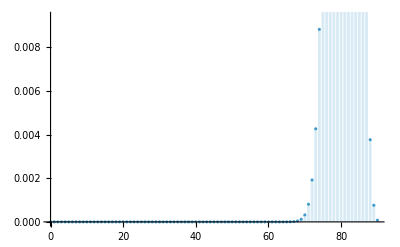

```mathematica
DiscretePlot[%,{k,0, 90}]
```